```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/y/Nutstore Files/1Project/1Qdia/code/Git/Fig4/Plot

```mathematica
lossPN2 = Import["N2lossPb8.0.txt","Data"];
epochmaxN2 = 500;
lossPN2⟦All,2⟧=lossPN2⟦All,2⟧/epochmaxN2
lossPN2⟦All,6⟧ = lossPN2⟦All,6⟧/lossPN2⟦1,8⟧
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

{0.814389,0.825338,0.87392,0.931932,0.969466,0.988092,0.995819,0.998598,0.999535,0.999842,0.999939,0.999969,0.999982,0.999988,0.999992,0.999995,0.999998,0.999999,0.999999,1.,0.999999}

```mathematica
lossPN3 = Import["N3lossPb20.0.txt","Data"];
epochmaxN3 = 2000;
lossPN3⟦All,2⟧=lossPN3⟦All,2⟧/epochmaxN3
lossPN3⟦All,6⟧ = lossPN3⟦All,6⟧/lossPN3⟦1,8⟧
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

{0.862199,0.986099,0.993291,0.996656,0.997984,0.998669,0.999139,0.999487,0.999725,0.999867,0.999941,0.999978,0.999991,0.999998,0.999998,0.999997,1.,1.,1.,1.,1.}

```mathematica
lossPN4 = Import["N4lossPb40.0.txt","Data"];
epochmaxN4 = 1500;
lossPN4⟦All,2⟧=lossPN4⟦All,2⟧/epochmaxN4;
lossPN4⟦All,6⟧ = lossPN4⟦All,6⟧/lossPN4⟦1,8⟧
```

{0.805145,0.959079,0.978814,0.986016,0.989384,0.991523,0.992975,0.994017,0.994831,0.995518,0.996118,0.996642,0.997097,0.997489,0.997824,0.998111,0.99836,0.998569,0.998749,0.998903,0.999034}

```mathematica
lossPN5 = Import["N5lossPb75.0.txt","Data"];
epochmaxN5 = 5000;
lossPN5⟦All,2⟧=lossPN5⟦All,2⟧/epochmaxN5
lossPN5⟦All,6⟧ = lossPN5⟦All,6⟧/lossPN5⟦1,8⟧
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,4999/5000}

{0.731702,0.973764,0.989918,0.994609,0.996205,0.99693,0.997504,0.997927,0.998243,0.9985,0.998698,0.99884,0.99896,0.999053,0.999139,0.999201,0.999246,0.999279,0.999303,0.999328,0.999357}

```mathematica
lossResN2=lossPN2⟦All,{2,4}⟧;
PsqureResN2 = lossPN2⟦All,{2,6}⟧;
PurityResN2 = lossPN2⟦All,{2,8}⟧;
offDResN2= lossPN2⟦All,{2,10}⟧;
```

```mathematica
lossResN3=lossPN3⟦All,{2,4}⟧;
PsqureResN3 = lossPN3⟦All,{2,6}⟧;
PurityResN3 = lossPN3⟦All,{2,8}⟧;
offDResN3= lossPN3⟦All,{2,10}⟧;
```

```mathematica
lossResN4=lossPN4⟦All,{2,4}⟧;
PsqureResN4 = lossPN4⟦All,{2,6}⟧;
PurityResN4 = lossPN4⟦All,{2,8}⟧;
offDResN4= lossPN4⟦All,{2,10}⟧;
```

```mathematica
lossResN5=lossPN5⟦All,{2,4}⟧;
PsqureResN5 = lossPN5⟦All,{2,6}⟧;
PurityResN5 = lossPN5⟦All,{2,8}⟧;
offDResN5= lossPN5⟦All,{2,10}⟧;
```

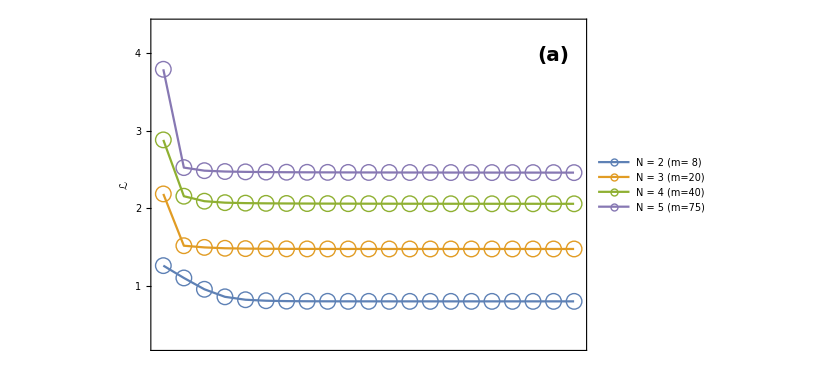

```mathematica
Figloss23=ListLinePlot[{lossResN2,lossResN3,lossResN4+10,lossResN4+10,lossResN5+10},PlotRange->{{-0.01,1.01},{0.256,4.35}},FrameLabel->{None,Style["ℒ",Italic,Directive[Large],Black,FontSize->20]},RotateLabel->False,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->Style["○",FontSize->16],
FrameTicks->{{{{0,"0.0"},{2.0,"2"},1,3,4},None},{None,None}},
PlotLegends->Placed[{Style["N = 2 (m= 8)",Bold,FontSize->14],Style["N = 3 (m=20)",Bold,FontSize->14],None,None},{0.4,0.74}],Epilog->Inset[Style["(a)",Bold,FontSize->20],{0.95,3.970}],
ImageSize->{620,291},ImagePadding->{{80,100},{1,10}}];
Figloss45=ListLinePlot[{lossResN2+10,lossResN3+10,lossResN4,lossResN4+10,lossResN5},PlotRange->{{-0.02,1.02},{0.256,4.35}},FrameLabel->{Style["Epoch/Epoch_max",Black,Directive[Large],FontSize->20],Style["ℒ",Italic,Directive[Large],Black,FontSize->20]},RotateLabel->False,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->Style["○",FontSize->16],
FrameTicks->{{{{0,"0.0"},{2.0,"2"},1,3,4},None},{{{0,"0.0"},0.2,0.4,0.6,0.8,{1.0,"1.0"}},None}},
PlotLegends->Placed[{None,None,Style["N = 4 (m=40)",Bold,FontSize->14],None,Style["N = 5 (m=75)",Bold,FontSize->14]},{0.7,0.74}],Epilog->Inset[Style["(a)",Bold,FontSize->20],{0.95,3.970}],
ImageSize->{600,360},ImagePadding->{{80,100},{60,0}}];
Figa = Show[Figloss23,Figloss45]
```

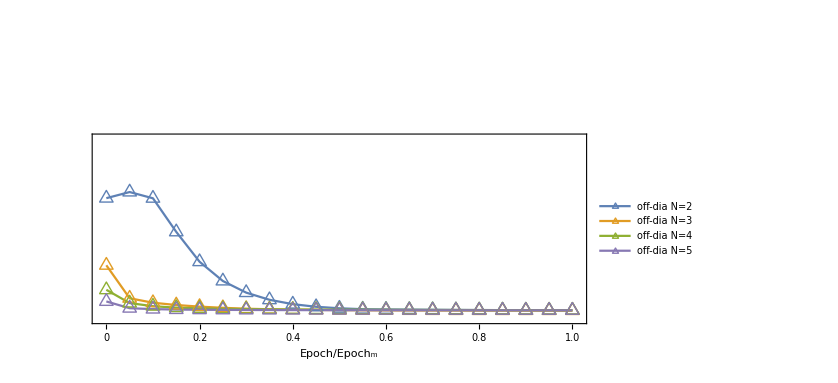

```mathematica
FigoffD=ListLinePlot[{offDResN2,offDResN3,offDResN4,lossResN2+1,offDResN5},PlotRange->{{-0.01,1.01},{-0.003,0.055}},FrameLabel->{{None,Style["(|ρ_(('_(off-dia))_)|)^(—————–)",Italic,Directive[Large],Black,FontSize->20]},{Style["Epoch/Epoch_m",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["△",FontSize->16]},
FrameTicks->{{None,{{0,"0.00"},0.01,0.020,0.03,0.04,0.05,0.8,{1.0,"1.0"}}},{{0,0.2,0.4,0.6,0.8,{1.0,"1.0"}},None}},
PlotLegends->Placed[{Style["off-dia N=2",Bold,FontSize->14],Style["off-dia N=3",Bold,FontSize->14],Style["off-dia N=4",Bold,FontSize->14],None,Style["off-dia N=5",Bold,FontSize->14]},{0.75,0.505}],
Epilog->Inset[Style["(b)",Bold,FontSize->20],{0.95,0.22}],
ImageSize->{620,340},ImagePadding->{{80,100},{60,0}}]
```

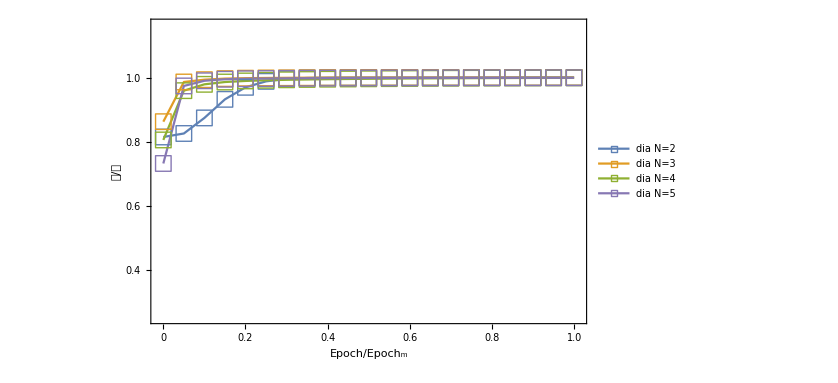

```mathematica
FigDia=ListLinePlot[{PsqureResN2,PsqureResN3,PsqureResN4,lossResN2+1,PsqureResN5},PlotRange->{{-0.01,1.01},{0.25,1.164}},FrameLabel->{{Style["𝒟/𝒫",Italic,Directive[Large],Black,FontSize->20],None},{Style["Epoch/Epoch_m",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["□",FontSize->16]},
FrameTicks->{{{{0,"0.0"},0.1,0.2,0.4,0.6,0.8,{1.0,"1.0"}},None},{{0,0.2,0.4,0.6,0.8,{1.0,"1.0"}},None}},
PlotLegends->Placed[{Style["dia N=2",Bold,FontSize->14],Style["dia N=3",Bold,FontSize->14],Style["dia N=4",Bold,FontSize->14],None,Style["dia N=5",Bold,FontSize->14]},{0.48,0.5}],
ImageSize->{620,340},ImagePadding->{{80,100},{60,0}}]
```

```mathematica
Figb=Overlay[{FigDia,FigoffD}]
```

-Graphics--Graphics-

```mathematica
Fig=Grid[{{Figa},{Figb}},Spacings->{Automatic, -0.8}]
```

-Graphics-
-Graphics--Graphics-

```mathematica
Export["Fig4.pdf",Fig]
```

Fig4.pdf